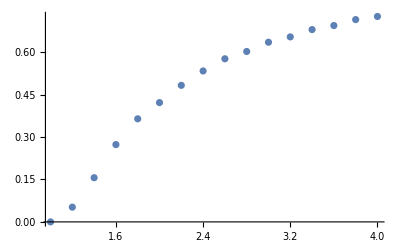

```mathematica
b={{1,0/(1×32)}, {1.2,2/(1.2×32)},{1.4,7/(1.4×32)},{1.6,14/(1.6×32)}, {1.8,21/(1.8×32)},{2,27/(2×32)},{2.2,34/(2.2×32)},{2.4,41/(2.4×32)},{2.6,48/(2.6×32)},{2.8,54/(2.8×32)},{3,61/(3×32)},{3.2,67/(3.2×32)},{3.4,74/(3.4×32)},{3.6,80/(3.6×32)},{3.8,87/(3.8×32)},{4,93/(4×32)}};
ListPlot[b]
```

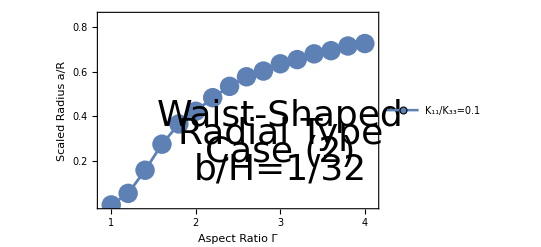

```mathematica
ListPlot[{b},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{1,1.5,2,2.5,3,3.5,4},None}}, PlotRange->{{0.9,4.1},{0,0.85}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{3.0,0.4}],Text[Style["Radial Type",Directive[Black,36]],{3.0,0.32}],Text[Style["Case (2)",Directive[Black,36]],{3.0,0.24}],Text[Style["b/H=1/32",Directive[Black,36]],{3.0,0.16}]}]
```